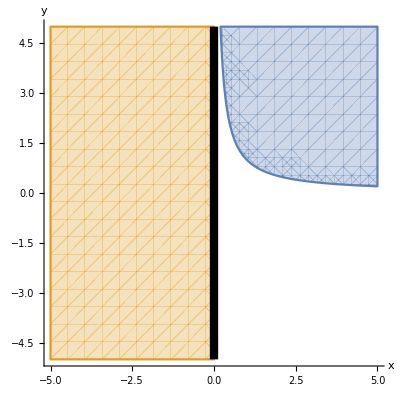

```mathematica
Show[RegionPlot[{1<=x y&&x≥0,x ≤0},{x,-5,5},{y,-5,5},Frame->False,Axes->True],Graphics[{Thickness[.015],Line[{{0,-5},{0,5}}]}], AxesLabel->{"x","y"}]
```

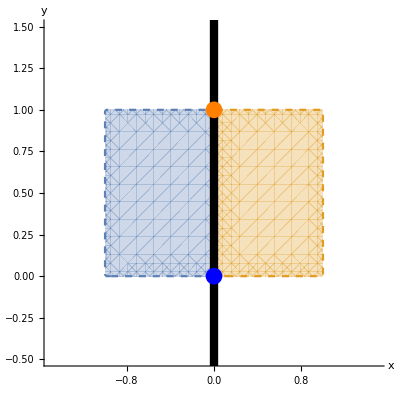

```mathematica
Show[RegionPlot[{-1≤x<0&&0≤y≤1,0<x≤ 1&&0≤y≤1},{x,-1.5,1.5},{y,-.5,1.5},Frame->False,Axes->True,BoundaryStyle->Dashed],Graphics[{Thickness[.015],Line[{{0,-5},{0,5}}]}],Graphics[{Blue,PointSize[.03],Point[{0,0}]}],Graphics[{Orange,PointSize[.03],Point[{0,1}]}], AxesLabel->{"x","y"}]
```

```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.